# Formats of periods

First, input the numbers (a_1,a_2) to choose which torus, and specify the radius of the open ball. The variable ‘relevantpoint’ has entries (LCS,Conifold,Infinity), where we put 1 for the point around which we compute the periods, and 0 for the other points.

```mathematica
Clear["`*"]
a1=1/6;
a2=5/6;
κ=1;
relevantpoint={0,0,1};
DomainRadius = Pi/6;
```

## Picard-Fuchs Equation

We bring the Picard-Fuchs equation into its form as a connection:

```mathematica
$Assumptions={z≠0,z≠1};
deriv[z_]:=z*D[#,z]&;
```

```mathematica
picardfuchs[z_]:=θ^2-z*(θ+a1)(θ+a2);
reducedpicardfuchs[z_]:=picardfuchs[z]/Coefficient[picardfuchs[z],θ^2]
coefflist=CoefficientList[reducedpicardfuchs[z],θ]//FullSimplify
PFfunctional=Collect[{f[z],deriv[z]@f[z],deriv[z]@deriv[z]@f[z]}.coefflist//Simplify,{f[z],f'[z],f''[z]}]
```

{(5 z)/(36 (-1+z)),z/(-1+z),1}

(5 z f[z])/(36 (-1+z))+(z (-1+2 z) f'[z])/(-1+z)+z^2 f''[z]

The above PF equation is in local coordinates around z=0. Now we compute the PF equation around the other points, and generate a new coefficient list of the modified PF equation (in local coordinates). We then have to force the equation back into the form  giving us the relation between the coefficients. I solved them by hand for now but this can of course be automated.

```mathematica
PFConifold=Collect[PFfunctional/.{z->1-z}/.{f->Function[{z},f[1-z]]}//Simplify,{deriv[z]@deriv[z]@f[z],deriv[z]@f[z],f[z]}];
PFInfinity=Collect[PFfunctional/.{z->1/z}/.{f->Function[{z},f[1/z]]}//Simplify,{deriv[z]@deriv[z]@f[z],deriv[z]@f[z],f[z]}];
PFfull=relevantpoint.{PFfunctional,PFConifold,PFInfinity}//Simplify
PFCoefficients={Coefficient[PFfull,f''[z]],Coefficient[PFfull,f'[z]],Coefficient[PFfull,f[z]]};
a=PFCoefficients[[1]]/z^2;
b=PFCoefficients[[2]]/z-a;
c=PFCoefficients[[3]];
PF={1,b/a,c/a}.{θ^2,θ,1}//FullSimplify
```

(-5 f[z]+36 z^2 (f'[z]+(-1+z) f''[z]))/(36 (-1+z))

-5/(36 (-1+z))+θ (1/(-1+z)+θ)

By definition, the first row of the connection matrix consists of A_11 = 0, A_12 = 1. The second row is given by the Picard-Fuchs equation. Since we will add any function of z within the connection to our LN-chain later, we also compute a version of the connection matrix where we replace with some foresight F5=z/(1-z). I should properly check which is better, but for now take F5=1/(1-z) for the singularity at infinity.

```mathematica
ConnectionMatrixA={{0,1},{-Coefficient[PF,θ,0],-Coefficient[PF,θ,1]}}
ConnectionMatrixAChainLCS = {{0,1},{-F5*Coefficient[ConnectionMatrixA[[2,1]],z/(-1+z)],-F5*Coefficient[ConnectionMatrixA[[2,2]],z/(-1+z)]}}
ConnectionMatrixAChainInfty={{0,1},{F5*Coefficient[ConnectionMatrixA[[2,1]],1/(z-1)],F5*Coefficient[ConnectionMatrixA[[2,2]],1/(z-1)]}};
ConnectionMatrixAChain = If[relevantpoint[[3]]==1,ConnectionMatrixAChainInfty,ConnectionMatrixAChainLCS]
```

{{0,1},{5/(36 (-1+z)),-1/(-1+z)}}

{{0,1},{0,0}}

{{0,1},{(5 F5)/36,-F5}}

## Monodromy

Write down the monodromy matrices and the corresponding log-monodromy matrices. For the point at infinity, the log of the monodromy matrix will return a logmonodromy matrix with eigenvalues between (-π,π) since Mathematica takes the principal branch. However, we want all the eigenvalues to be between 0 and 1 so that they correspond to , so we let Mathematica search a better log-monodromy matrix for us (which is guaranteed to exist).

```mathematica
MonodromyLCS={{1,1},{0,1}};
MonodromyConif={{1,0},{-κ,1}};
MonodromyInfty={{1-κ,-1},{κ,1}};
Monodromy=MonodromyLCS*relevantpoint[[1]]+MonodromyConif*relevantpoint[[2]]+MonodromyInfty*relevantpoint[[3]];
LogMonodromyLCS=1/(2Pi I)MatrixLog[MonodromyLCS];
LogMonodromyConif=1/(2Pi I)MatrixLog[MonodromyConif];
LogMonodromyInfty=1/(2Pi I)MatrixLog[MonodromyInfty];
(*CalculatedLogMonodromyInfty={t1,t2,t3,t4}/.FindInstance[Eigenvalues[{{t1,t2},{t3,t4}}]=={a1,a2}&&MatrixExp[2Pi I*{{t1,t2},{t3,t4}}]==Monodromy,{t1,t2,t3,t4}]//Flatten(* ugly way of doing it but dont know how to improve right now *) 
LogMonodromyInfty={{CalculatedLogMonodromyInfty[[1]],CalculatedLogMonodromyInfty[[2]]},{CalculatedLogMonodromyInfty[[3]],CalculatedLogMonodromyInfty[[4]]}};*)
LogMonodromy=relevantpoint[[1]]*LogMonodromyLCS+relevantpoint[[2]]*LogMonodromyConif+relevantpoint[[3]]*LogMonodromyInfty//FullSimplify
```

{{ⅈ/(6 √3),ⅈ/(3 √3)},{-ⅈ/(3 √3),-ⅈ/(6 √3)}}

## Ansatz

We now make the ansatz  with  holomorphic univalued, which then satisfies . Then we need to manually make this into the LN-chain system by appending an entry for F5 and the coordinate z. NOTE: F5 now has different chain depending on choice at infinity, reflected in the if statement.

```mathematica
Y={{y11,y12},{y21,y22}};
YConnection=ConnectionMatrixAChain.Y-Y.LogMonodromy//Flatten;
YVector=Y//Flatten;
YTable=Table[Coefficient[YConnection[[i]],YVector[[j]]],{i,1,4},{j,1,4}];
YTemp=Map[Prepend[#,0]&,YTable];
YTemp2=Map[Append[#,0]&,YTemp];
YwithCoord=Join[{{1,0,0,0,0,0}},YTemp2]; (*prepend z d_z z = z *)
YChain=If[relevantpoint[[3]]==1,Join[YwithCoord,{{0,0,0,0,0,-F5}}],Join[YwithCoord,{{0,0,0,0,0,F5+1}}]]; (*append F5 *)
YChain//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/(6 √3) | ⅈ/(3 √3) | 1 | 0 | 0
0 | -ⅈ/(3 √3) | ⅈ/(6 √3) | 0 | 1 | 0
0 | (5 F5)/36 | 0 | -ⅈ/(6 √3)-F5 | ⅈ/(3 √3) | 0
0 | 0 | (5 F5)/36 | -ⅈ/(3 √3) | ⅈ/(6 √3)-F5 | 0
0 | 0 | 0 | 0 | 0 | -F5)

Thus the LN system is given by:

```mathematica
LNChainRHS=YChain.{F0,F1,F2,F3,F4,F5};
MatrixForm[z{D[F0[z],z],D[F1[z],z],D[F2[z],z],D[F3[z],z],D[F4[z],z],D[F5[z],z]}]==MatrixForm[LNChainRHS]
```

(z F0'[z]
z F1'[z]
z F2'[z]
z F3'[z]
z F4'[z]
z F5'[z])==(F0
-(ⅈ F1)/(6 √3)+(ⅈ F2)/(3 √3)+F3
-(ⅈ F1)/(3 √3)+(ⅈ F2)/(6 √3)+F4
(ⅈ F4)/(3 √3)+F3 (-ⅈ/(6 √3)-F5)+(5 F1 F5)/36
-(ⅈ F3)/(3 √3)+F4 (ⅈ/(6 √3)-F5)+(5 F2 F5)/36
-F5^2)

## LN-Format of Y(z)

We now compute the LN-format of  using the formula . Here the format of the domain U is given by the least integer upper bound of  where r is the radius of the disc. This still has to be converted from the radius of the open ball. The length N of the chain is 6 and the degrees of the polynomials can be found from the expression above, as well as their coefficients. The supremum requires some more care, since for this we need explicit expressions for the functions F0...F5.

```mathematica
DiskRadius=Sqrt[(Sec[DomainRadius])^2-1];
DomainFormat=Ceiling[1+DiskRadius];
ChainLength=6;
PolynomialSumDegree=Sum[ResourceFunction["PolynomialDegree"][LNChainRHS[[i]],{F0,F1,F2,F3,F4,F5,z}],{i,1,6}];
PolynomialCoefficients=Abs[CoefficientList[LNChainRHS,{F0,F1,F2,F3,F4,F5}]]//Flatten;
PolynomialSumCoefficients = Total[PolynomialCoefficients];
ω0=Hypergeometric2F1[a1,a2,1,z];
ω1=I/Sqrt[κ]*Hypergeometric2F1[a1,a2,1,1-z];
ExactSolLCS={{ω0,ω1},{z*D[ω0,z],z*D[ω1,z]}};
ExactSolConif={{ω0/.z->1-z,ω1/.z->1-z},{z*D[ω0/.z->1-z,z],z*D[ω1/.z->1-z]}};
ExactSolInfty={{ω0/.z->1/z,ω1/.z->1/z},{z*D[ω0/.z->1/z,z],z*D[ω1/.z->1/z]}};
ExactSol = relevantpoint[[1]]*ExactSolLCS+relevantpoint[[2]]*ExactSolConif+relevantpoint[[3]]*ExactSolInfty
ExactY=ExactSol.MatrixExp[-Log[z]*LogMonodromy]//Flatten;
SupremumTerm=Max[Table[FindMaxValue[{Abs[ExactY][[i]],Abs[z]>0&&Abs[z]<DiskRadius},z],{i,1,4}]];
LNFormatChain=DomainFormat+ChainLength+PolynomialSumDegree+PolynomialSumCoefficients+SupremumTerm;
LNFormatY=LNFormatChain+2
```

{{Hypergeometric2F1[1/6,5/6,1,1/z],ⅈ Hypergeometric2F1[1/6,5/6,1,1-1/z]},{-(5 Hypergeometric2F1[7/6,11/6,2,1/z])/(36 z),ⅈ z Hypergeometric2F1[1/6,5/6,1,1-1/z]}}

FindMaxValue::steperr: Error in step computation.

27.6319

## LN,PF-Format of the period matrix

We compute the LN,PF-format of the period matrix by first converting the LN-format of Y to an LN,PF-format, and then combining it with the logarithmic term. We take the LN,PF-format of the complex logarithm as a given (elaborated in the thesis). The  term will be a polynomial of the form  with λ the eigenvalues of the log-monodromy matrix (which are always real). For the LCS and conifold points these eigenvalues are zero but for the point at infinity they are given by (1/6,5/6) as we insisted earlier. We did this because now z^λ is an LN function and we can simply add them to our chain, which will increase the length of the chain by 1, the sum over degrees of polynomials by 1, the sum over coefficients by λ, and the supremum term will become a maximum between the previous one and the supremum of z^λ. Finally we multiply out the ansatz to find the expressions for the entries of the period matrix. Now we have a format for each of the expressions appearing in it, and the full format can be most easily found by hand (it can of course be automated but I have decided not to do so for now) by taking appropriate maxima.

```mathematica
LNPFFormatLog=36;
LNPFFormatY=LNFormatY+12;
LNPFFormatza1Y=LNPFFormatY+1+1+a1-SupremumTerm+Max[{SupremumTerm,FindMaxValue[{Abs[z^a1],Abs[z]>0&&Abs[z]<DiskRadius},z]}];
LNPFFormatza2Y=LNPFFormatY+1+1+a2-SupremumTerm+Max[{SupremumTerm,FindMaxValue[{Abs[z^a2],Abs[z]>0&&Abs[z]<DiskRadius},z]}];
PeriodMatrix=Y.MatrixExp[Log[z]*LogMonodromy]
(*Attempt at automating; might return to this later: *)
PeriodMatrixPolyal = PeriodMatrix/.{z^a1->x1,z^a2->x2,Log[z]->x3}//FullSimplify;
CoefficientsPeriodMatrix = Table[CoefficientArrays[PeriodMatrixPolyal[[i,j]],{y11,y12,y21,y22,x1,x2,x3}],{i,1,2},{j,1,2}];(* In order to find the coefficient of a_i b_j we take [[3,1,i,j]] *)
```

{{y11 (1/(2 z^(1/6))-ⅈ/(2 √3 z^(1/6))+z^(1/6)/2+(ⅈ z^(1/6))/(2 √3))+y12 (ⅈ/(√3 z^(1/6))-(ⅈ z^(1/6))/(√3)),y12 (1/(2 z^(1/6))+ⅈ/(2 √3 z^(1/6))+z^(1/6)/2-(ⅈ z^(1/6))/(2 √3))+y11 (-ⅈ/(√3 z^(1/6))+(ⅈ z^(1/6))/(√3))},{y21 (1/(2 z^(1/6))-ⅈ/(2 √3 z^(1/6))+z^(1/6)/2+(ⅈ z^(1/6))/(2 √3))+y22 (ⅈ/(√3 z^(1/6))-(ⅈ z^(1/6))/(√3)),y22 (1/(2 z^(1/6))+ⅈ/(2 √3 z^(1/6))+z^(1/6)/2-(ⅈ z^(1/6))/(2 √3))+y21 (-ⅈ/(√3 z^(1/6))+(ⅈ z^(1/6))/(√3))}}

## LN,PF-Format of period mapping

Now we consider the period mapping τ=Π1/Π0. First we find its form in terms of the holomorphic and singular parts, and define the fundamental domain as well as the generators of the modular group.

```mathematica
FormatUnrestrictedPeriodMap=5;
PeriodMap=PeriodMatrix[[1,2]]/PeriodMatrix[[1,1]]//Simplify
PeriodMapExact=ExactSol[[1,2]]/ExactSol[[1,1]]
FundamentalDomain={x^2+y^2>1 &&-1/2<x<1/2&&y>0};
S=ReplaceAll[#,{x->-x/(x^2+y^2),y->(+y)/(x^2+y^2)}]&;
T=ReplaceAll[#,{x->x+1,y->y}]&;
Tinv=ReplaceAll[#,{x->x-1,y->y}]&;
```

(-2 √3 y11 (-1+z^(1/3))+y12 (3 ⅈ-√3+(3 ⅈ+√3) z^(1/3)))/(2 √3 y12 (-1+z^(1/3))+y11 (3 ⅈ+√3-(-3 ⅈ+√3) z^(1/3)))

(ⅈ Hypergeometric2F1[1/6,5/6,1,1-1/z])/Hypergeometric2F1[1/6,5/6,1,1/z]

We plot the exact solution, along with the fundamental domain and some translates of it. The user should decide how many of these to include by inspecting the graph (note that the inverse of S is simply S so it has not been included). Note that due to the fact that the singularities of the period mapping are logarithmic, they are extremely sharp and Mathematica has trouble plotting them accurately. Thus, near the (images of the) singularities the plot generated by Mathematica should not be trusted too much. One could play with the values for PlotPoints and MaxRecursion, as well as the lower bound for the radius, to improve this slightly. This first example generates the fundamental domain of the modular group PSL(2,Z). The fundamental domains of the congruence subgroups of it are given by unions of it with some translates. We explicitly construct them in the next section.

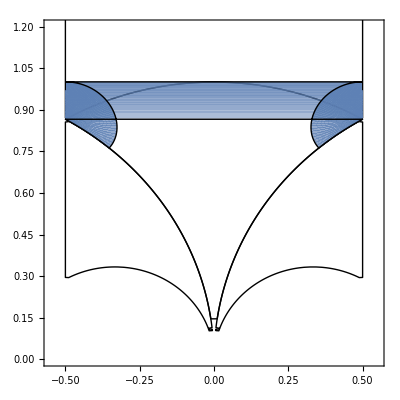

```mathematica
Show[RegionPlot[{FundamentalDomain,Evaluate[S@FundamentalDomain],Evaluate[T@S@T@S@FundamentalDomain],Evaluate[Tinv@S@Tinv@S@FundamentalDomain]},{x,-2,2},{y,0,2},PlotPoints->100,MaxRecursion->3,PlotStyle->Opacity[0],BoundaryStyle->{Black,AbsoluteThickness->1.6},PlotRange->{{-0.55,0.55},{0,1.2}}],ParametricPlot[{Re[PeriodMapExact/.z->r*Exp[I ϕ]],Im[PeriodMapExact/.z->r*Exp[I ϕ]]},{r,10^(-12),DiskRadius},{ϕ,0,2Pi},PlotPoints->100,MaxRecursion->4,BoundaryStyle->{Black,Thick}]]
```

In order to count the number of translates of the fundamental domains of the congruence subgroup we use the fact that the monodromy matrices act as their generators, meaning we replace S and T with the corresponding action of the monodromy matrices on τ via . For the fundamental domain of the modular curve  we need κ translates of the fundamental domain by the monodromy group (or rather, a coset representative of it).

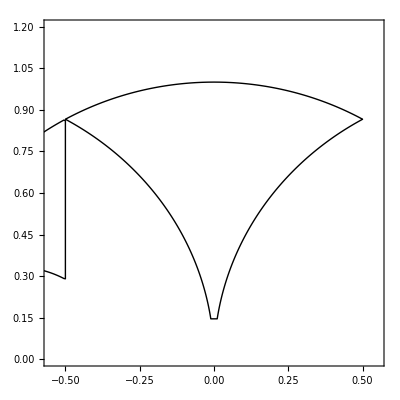

```mathematica
MatrixToOperator=Assuming[{Element[x,Reals],Element[y,Reals]},ReplaceAll[#,{x->Re[(m11(x+I y)+m12)/(m21(x+ I y)+m22)],y->Im[(m11(x+I y)+m12)/(m21(x+ I y)+m22)]}]&//Simplify];
CosetRep1=MatrixToOperator/.{m11->0,m12->-1,m21->1,m22->0};
CosetRep2=MatrixToOperator/.{m11->1,m12->0,m21->1,m22->1};
CosetRep3=MatrixToOperator/.{m11->0,m12->-1,m21->1,m22->2};
CosetRep4=MatrixToOperator/.{m11->0,m12->-1,m21->1,m22->3};
CosetRep5=MatrixToOperator/.{m11->1,m12->0,m21->2,m22->1};
IndexVector={1,2,3,5};
CosetReps={CosetRep1,CosetRep2,CosetRep3,CosetRep4,CosetRep5};
Through[CosetReps@FundamentalDomain];
RegionPlot[Evaluate@Through[CosetReps[[1;;IndexVector[[2]]]]@FundamentalDomain],{x,-2,2},{y,0,2},PlotPoints->100,MaxRecursion->3,PlotStyle->Opacity[0],BoundaryStyle->{Black,AbsoluteThickness->1.6},PlotRange->{{-0.55,0.55},{0,1.2}}]
```

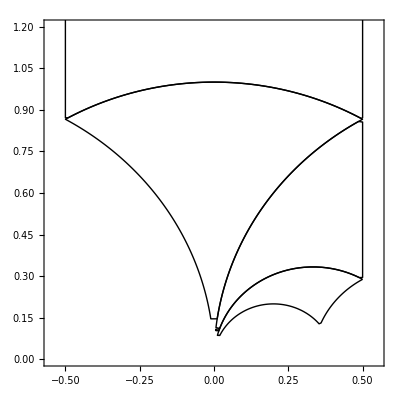

```mathematica
RegionPlot[{FundamentalDomain,Evaluate[S@FundamentalDomain],Evaluate[S@T@FundamentalDomain],Evaluate[Tinv@S@Tinv@S@T@FundamentalDomain]},{x,-2,2},{y,0,2},PlotPoints->100,MaxRecursion->3,PlotStyle->Opacity[0],BoundaryStyle->{Black,AbsoluteThickness->1.6},PlotRange->{{-0.55,0.55},{0,1.2}}]
```

```mathematica
MonodromyInfty.MonodromyInfty.MonodromyInfty.MonodromyInfty.MonodromyInfty.MonodromyInfty
```

{{1,0},{0,1}}

```mathematica
Eigenvalues[LogMonodromy]
```

{-1/6,1/6}

```mathematica
DSolve[PFfunctional==0,f,z]
```

{{f→Function[{z},C[1] LegendreP[-1/6,-1+2 z]+C[2] LegendreQ[-1/6,-1+2 z]]}}